```mathematica
diffEq=D[ψ[x,t],t]==𝒟 D[ψ[x,t],{x,2}]
```

ψ^(0,1)[x,t]==𝒟 ψ^(2,0)[x,t]

```mathematica
ψ0[x_]:=1-x
```

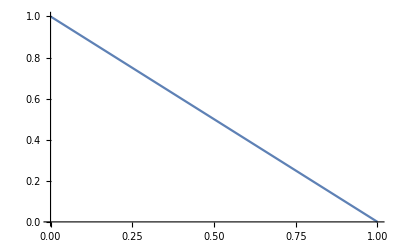

```mathematica
Plot[ψ0[x],{x,0,1},PlotRange->{0,1}]
```

```mathematica
bc0=ψ[0,t]==1-t
```

ψ[0,t]==1-t

```mathematica
bc1=ψ[1,t]==0
```

ψ[1,t]==0

```mathematica
bc2=ψ[x,0]==ψ0[x]
```

ψ[x,0]==1-x

```mathematica
sol=DSolve[{diffEq,bc0,bc1,bc2},ψ[x,t],{x,t}]
```

{{ψ[x,t]→(-1+t) (-1+x)+((2-2 ⅇ^(-π^2 t 𝒟 K[1]^2)) Sin[π x K[1]])/(π^3 K[1]^3)K[1]1∞}}

```mathematica
f[x_,t_,𝒟_]:=(t-1)(x-1)+∑_(k=1)^100 (2(1-ⅇ^(-π^2 t 𝒟 k^2))Sin[k π x])/(π^3 k^3)
```

```mathematica
𝒟0=1
```

1

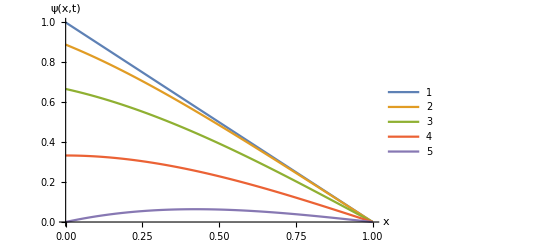

```mathematica
Plot[{f[x,0,𝒟0],f[x,1/9,𝒟0],f[x,3/9,𝒟0],f[x,6/9,𝒟0],f[x,9/9,𝒟0]},{x,0,1},PlotRange->{0,1},AxesLabel->{"x","ψ(x,t)"},PlotLegends->Automatic]
```